This notebook simulates a self-regulated gene with the Chemical Langevin Equation (CLE) implemented by Yan et al 2017. Particularly, the CLE for burst in protein but no in mRNA (CLE2).

## Parameters

These are the ranges of values for parameters variation. The range of each parameter is divided into smaller ranges (subRanges). In this way the complete range is evaluated in parallel files each one with a subRange of parameters values.

```mathematica
iteraciones=5000; (* Number of algorithm iterations *)
replicas=10;  (* Number of times the algorithm is run *)
name=0.5;(* This is the last value of the range for the parameter being evluated *)
kgs=Range[0.01,1,0.01];
γgs=Range[0.02,name,0.02]; (* subRanges: 0.02-0.5, 0.52-1.0, 1.02-1.5, 1.52-2 *)
γms=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
γps=Range[0.001,0.1(*name*),0.001];(* subRanges: 0.001-0.025, 0.026-0.05, 0.051-0.075, 0.076-0.1 *)
parametro="γg";
```

```mathematica
Clear[kg,γg,bm,km,γm,kp,γp,τ,ϵ,g,nc];
kg=0.01158;(* Gene activation rate (t^-1)*)
γg= 2.082;(* Gene desactivation rate (t^-1) *)
km=0.696;(* Production rate of mRNA (molecules*t^-1) *)
bm=km/(γg+kg);(* Burst size mean (molecules-mRNA) *)
γm=0.02082;(* Degradation rate (molecules*t^-1) *)
kp=1.386;(* Production rate of proteins (molecules*t^-1) *)
γp=0.02082 ;(* Degradation rate (molecules*t^-1) *)
bp=kp/γm;(* Burst size mean (molecules-protein) *)
kaa=γg/kg; (* Michaelis-Mente constant *)
h=3; (* Hill's constant *)
ϵ=0.03; (* First control parameter_ the change in the propensity function or in the number of molecules in a step τ is bounded by this number *)
g={1};(* Highest order of reaction in which specie i appears as a reactant, for these cases production and degradation are the Fisrt Order*)
nc=10; (* second control parameters_ indicates the maximum number of fires for a reaction be considered as a critical one *)
species:={protein}; (* The values of these are changing in each step τ*)
```

```mathematica
(* NOTA IMPORTANTE: kp y γp no pueden ser exactamente iguales *)
```

## Burst in protein but no-mRNA

### Functions

```mathematica
numero=0.01; (* Basal transcription *)
autoActivation[activator_,γg_,kg_,h_]:=(activator^h/((γg/kg)+activator^h));  (* self-regulation Hill function *)
ff1[dato_]:=N[Variance[dato]/Mean[dato]];  (* FF for noise meadure *)
expressionNoise[data_]:=N[Variance[data]/Mean[data]^2](* CV2 for noise meadure *)
```

```mathematica
(* CLE for promoter activity *)
equPromotor[promotor_,kg_,γg_,regulation_,τ_]:=Module[{promotors},promotors=promotor+kg(1-promotor)*regulation*τ-γg*promotor*τ; If[MatchQ[promotors,_Complex]||promotors<0,numero,promotors]]

(* CLE for protein expression*)
equProtein[protein_,promotor_,km_,bp_,γp_,τ_]:=Module[{rnd1=RandomVariate[NormalDistribution[0,1]],rnd2=RandomVariate[NormalDistribution[0,1]],proteins},proteins=protein+(promotor*km* bp* τ+(promotor*km* bp* τ(2 bp +1))^(1/2)rnd1 )-(γp protein τ+(γp protein τ)^(1/2)  rnd2); If[MatchQ[proteins,_Complex]||proteins<0,numero,proteins]];

(* Algorithm to select τ or Δt *)
τChoicee[promotor_,protein_,regulation_,kg_,γg_,km_,bp_,γp_]:=Module[{allμvarNC,τ1,promotori,proteini},
promotori=If[promotor==0,numero,promotor];
proteini=If[protein==0,numero,protein];
(* reactionsVandPF={{{1,kg*bm},{-1,γm*mRNAi}},{{1,kp*proteini},{-1,γp*proteini}}}For each specie introduce the state change value (v) and the propensity (PF) of synthesis and degradation reactions: {{v,PF}-synthesis,{v,PF}-degradation}-specie *);
allμvarNC={{promotori,kg(1-promotori)*regulation,kg(1-promotori)*regulation},{promotori,-γg*promotori,γg*promotori},{proteini,promotori*km* bp,promotori*km* bp},{proteini,-γp*proteini,γp*proteini}};
τ1={Sequence@@Table[Min[Max[ϵ i[[1]]/g,1]/Abs[i[[2]] ],Max[ϵ i[[1]]/g,1]^2/i[[3]]],{i,allμvarNC[[3;;4]]}],Min[Max[ϵ promotori/g,1]/Abs[allμvarNC[[1,2]]],Max[ϵ promotori/g,1]^2/allμvarNC[[1,3]]],1/(γp*promotori)Log[1/(1-RandomReal[{0,1}])]};(*ESTO SALE DEL ARTÍCULO DE Cao 2016 y CHING-YAN 2017. Para cada especie se calcula el tao. Cuando ambas reacciones son no-crticas este se calcula con la suma de la media y la varianza de ambas reacciones. Cuando la degradación se torna critica estas se separan. Cuando hay burst se calcula una tipo de tao para el burst y otro para la degradación (uno cuando es no-critica y otro cuando es critica) *)
Min[τ1[[1]],
If[proteini≥10,τ1[[2]],1/(γp*proteini)Log[1/(1-RandomReal[{0,1}])]] (*ESTO SALE DEL ARTÍCULO DE Cao 2016*),τ1[[3]],τ1[[4]]
]]
```

### Solution-iteration

```mathematica
proteinffcv2List={};
Table[
listEstimateprotein={};
listDataTprotein={};
timesT={};
Table[
promotor=0.9;
promotorlist={0.9};
protein=1;
proteinlist={1};
t=0;
tlist={0};
Do[
τ=τChoicee[promotor,protein,autoActivation[protein,γg,kg,h],kg,γg,km,kp/γm,γp];
t=t+τ;
AppendTo[tlist,t];
promotor=equPromotor[promotor,kg,γg,autoActivation[protein,γg,kg,h],τ];
AppendTo[promotorlist,promotor];
protein=equProtein[protein,promotor,km,kp/γm,γp,τ];
AppendTo[proteinlist,protein];
Print["kg:",kg," γg:",γg," pro:",promotor," protein:",protein],iteraciones];
proteinffcv2It=Table[{ff1[Flatten@i],expressionNoise[Flatten@i]},{i,
{proteinlist[[1000;;All]]}}];
AppendTo[listEstimateprotein,proteinffcv2It],replicas];
AppendTo[proteinffcv2List,Mean[listEstimateprotein]],{kg,kgs},{γg,γgs}(*,{γm,γms}*)];
```

```mathematica
Export["burstPRCLE_"<>parametro<>ToString[name],proteinffcv2List,"CSV"];
```

### Reviewing

```mathematica
Flatten[proteinffcv2List,1]
```

{{79.129,0.0553098},{86.1561,0.0848176},{94.5288,0.107553},{87.6318,0.0521443},{70.2524,0.0487965},{84.3396,0.0705772}}

```mathematica
label="FF: "<>ToString[proteinffcv2List[[1,1,1]]]<>" kon: 0.02, koff: 0.5, ksm: 0.696, kdm: 0.02, \nksp: 1.386, kdp:0.0282, CLE One G R, primeras ";
```

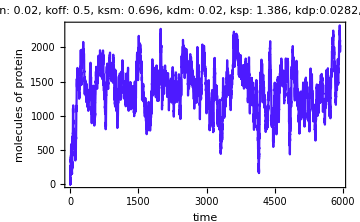

```mathematica
datesList=Transpose[{tlist,proteinlist}];ListLinePlot[datesList[[1;;-1]],Frame-> True,PlotStyle->
RGBColor[0.3,.1,1],ImageSize->Medium,FrameLabel->{"time","molecules of protein"},PlotLabel->label]
```

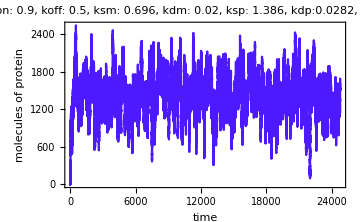

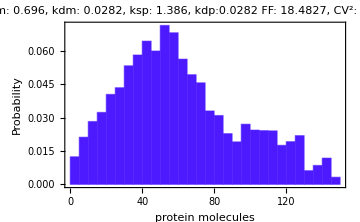

```mathematica
distribución=Flatten@listDataT[[All,All,2]];
Histogram[distribución,"Scott","Probability",Frame->True,FrameLabel->{"protein molecules","Probability"},PlotLabel->" kon:1, koff:2, ksm: 0.696, kdm: 0.0282, \nksp: 1.386, kdp:0.0282"<>" FF: "<>ToString[ff1[distribución]]<>", CV^2: "<>ToString[expressionNoise[distribución]]<>", Mean: "<>ToString[Mean[distribución]//N],ChartStyle->RGBColor[0.3,.1,1],ImageSize->Medium]
```

## References

Yan C - CS, Chepyala SR, Yen C - M, Hsu C - P . Efficient and flexible implementation of Langevin simulation for gene burst production . Sci Rep . 2017; 7 : 16851. doi : 10.1038/s41598 - 017 - 16835 - y